```mathematica
ϕ[n_]:=π^(-1/4)*(1/Sqrt[(2^n)*(n!)])*Exp[-0.5*y^2]*HermiteH[n,y];
```

```mathematica
Pϵ=Table[NIntegrate[y^4*ϕ[n]^2,{y,-50,50},MaxRecursion->20,AccuracyGoal->4],{n,0,50}];
```

```mathematica
NIntegrate[y^4*ϕ[51]^2,{y,-∞,∞},MaxRecursion->20,AccuracyGoal->4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3978.75

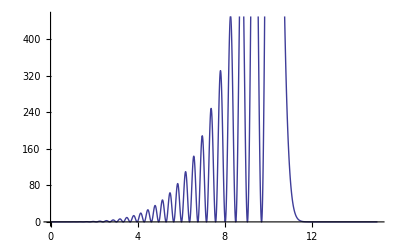

```mathematica
Plot[y^4*ϕ[55]^2,{y,0,15}]
```

```mathematica
Integrate[y^4*ϕ[10]^2,{y,-∞,∞}]
```

165.75

```mathematica
Export["Pe.txt",Pϵ,"Table"]
```

Pe.txt

```mathematica
Pϵ
```

{0.75,3.75,9.75,18.75,30.75,45.75,63.75,84.75,108.75,135.75,165.75,198.75,234.75,273.75,315.75,360.75,408.75,459.75,513.75,570.75,630.75,693.75,759.75,828.75,900.75,975.75,1053.75,1134.75,1218.75,1305.75,1395.75,1488.75,1584.75,1683.75,1785.75,1890.75,1998.75,2109.75,2223.75,2340.75,2460.75}